Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210507_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_347418.csv"];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/21,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
step11=11;
step12=11;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,step11,win1];]
```

{110.803,Null}

```mathematica
graphsandnodenumbers1=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers1[[i]][[1]],FindGraphCommunities[graphsandnodenumbers1[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers1}];
```

```mathematica
singlerandomgraphsdegfxd1=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomerdrenmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphsdegfxd1[[i]],FindGraphCommunities[singlerandomgraphsdegfxd1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd1}];
singlerandomgraphscomm1=Table[randomizinggraphmod[i],{i,graphsandnodenumbers1[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm1[[i]],FindGraphCommunities[singlerandomgraphscomm1[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm1}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity1=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers1[[All,1]]}];]
```

{388.27,Null}

```mathematica
bucketnode11=graphsandnodenumbers1[[All,2]]
```

{70,81,84,84,88,86,84,77,82,82,76,78,81,86,85,83,83,87,87}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,step12,win2];]
```

{88.4789,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{56,66,69,70,73,67,68,72,76,78,81,73,66,75,68,62,71,67,70,72,63,72,74,65,67,63,71,74,78,75,78,77,70,66,73,74,78,75,67,78,81}

```mathematica
(* AbsoluteTiming[widthdatafullFixedstep1=snetworkdatabinned[9,step1,datafull];
graphsandnodenumbersdatafull1=snetworkgraph[widthdatafullFixedstep1[[1]],widthdatafullFixedstep1[[2]],2,7,400,Green];]
randomnessvalues1=randomnessvaluesformodularitytwonullmodel[graphsandnodenumbersdatafull1[[1]]];*)
```

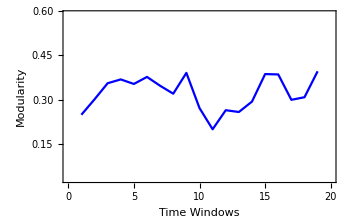
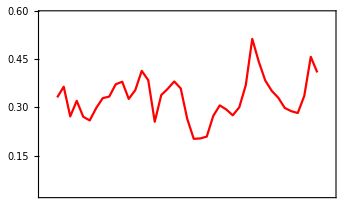
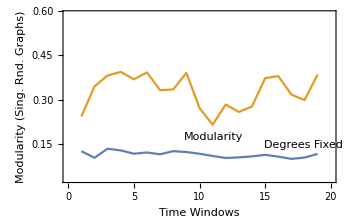
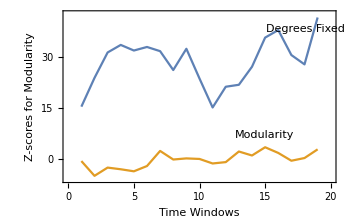

```mathematica
modularityplotrange={0.03,0.59};(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues12}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues1}],Thread[{Range@win1,singlerandomcommmodularityvalues1}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity1[[All,1]]}],Thread[{Range@win1,Zscoresmodularity1[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity1],1]},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
step21=1;
step22=1;
```

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,step21,win1];]
```

{20.6577,Null}

```mathematica
graphsandnodenumbers2=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers2[[i]][[1]],FindGraphCommunities[graphsandnodenumbers2[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers2}];
```

```mathematica
singlerandomgraphsdegfxd2=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomerdrenmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphsdegfxd2[[i]],FindGraphCommunities[singlerandomgraphsdegfxd2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd2}];
singlerandomgraphscomm2=Table[randomizinggraphmod[i],{i,graphsandnodenumbers2[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm2[[i]],FindGraphCommunities[singlerandomgraphscomm2[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm2}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity2=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers2[[All,1]]}];]
```

{153.069,Null}

```mathematica
bucketnode21=graphsandnodenumbers2[[All,2]]
```

{23,24,24,15,22,22,19,20,16,19,22,21,22,15,18,20,14,10,12}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,step22,win2];]
```

{18.0395,Null}

```mathematica
graphsandnodenumbers22=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues22=Table[N@GraphAssortativity[graphsandnodenumbers22[[i]][[1]],FindGraphCommunities[graphsandnodenumbers22[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers22}];
```

```mathematica
bucketnode22=graphsandnodenumbers22[[All,2]]
```

{23,18,11,10,23,24,15,14,12,12,13,19,20,12,9,17,17,14,15,11,19,16,12,12,12,16,16,12,11,8,8,11,15,17,10,10,9,9,8,8,11}

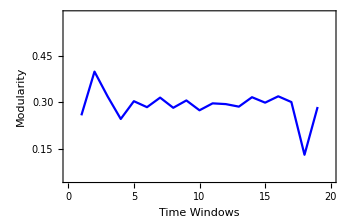
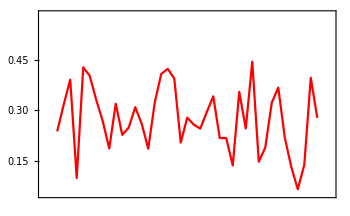
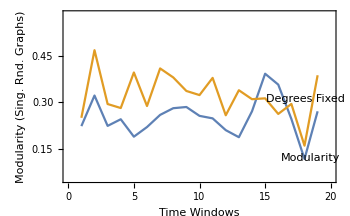
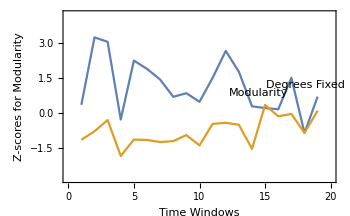

```mathematica
modularityplotrange={0.05246,0.584368};(* MinMax[{modularityvalues2,singlerandomcommmodularityvalues2,singlerandomerdrenmodularityvalues2,modularityvalues22}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues22}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues2}],Thread[{Range@win1,singlerandomcommmodularityvalues2}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity2[[All,1]]}],Thread[{Range@win1,Zscoresmodularity2[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity2],1]},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Above}]]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,bucketnode11,win1];]
```

{9.1364,Null}

```mathematica
bucketsize3=Flatten@widthdataintimewindowsFixedbucket1[[4]]
```

{497,429,414,414,395,404,414,452,424,424,458,446,429,404,409,419,419,400,400}

```mathematica
graphsandnodenumbers3=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues3=Table[N@GraphAssortativity[graphsandnodenumbers3[[i]][[1]],FindGraphCommunities[graphsandnodenumbers3[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers3}];
```

```mathematica
singlerandomgraphsdegfxd3=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomerdrenmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphsdegfxd3[[i]],FindGraphCommunities[singlerandomgraphsdegfxd3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd3}];
singlerandomgraphscomm3=Table[randomizinggraphmod[i],{i,graphsandnodenumbers3[[All,1]]}];
singlerandomcommmodularityvalues3=Table[N@GraphAssortativity[singlerandomgraphscomm3[[i]],FindGraphCommunities[singlerandomgraphscomm3[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm3}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity3=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers3[[All,1]]}];]
```

{476.672,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,bucketnode12,win2];]
```

{9.19325,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{296,251,240,237,227,247,244,230,218,213,205,227,251,221,244,267,234,247,237,230,263,230,224,255,247,263,234,224,213,221,213,215,237,251,227,224,213,221,247,213,205}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

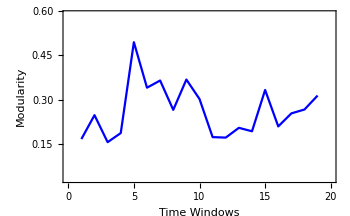
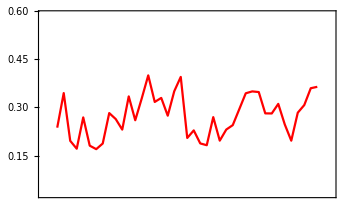
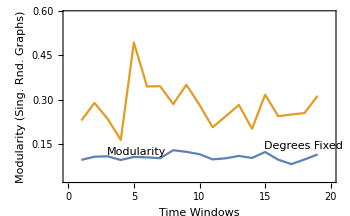
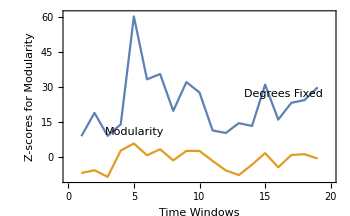

```mathematica
modularityplotrange={0.03,0.59};(* MinMax[{modularityvalues3,singlerandomcommmodularityvalues3,singlerandomerdrenmodularityvalues3,modularityvalues32}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues3}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues32}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues3}],Thread[{Range@win1,singlerandomcommmodularityvalues3}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity3[[All,1]]}],Thread[{Range@win1,Zscoresmodularity3[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity3],1]},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Above}]]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,bucketnode21,win1];]
```

{8.28694,Null}

```mathematica
bucketsize4=Flatten@thicknessdataintimewindowsFixedbucket1[[4]]
```

{1511,1448,1448,2317,1580,1580,1829,1738,2172,1829,1580,1655,1580,2317,1931,1738,2482,3475,2896}

```mathematica
graphsandnodenumbers4=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues4=Table[N@GraphAssortativity[graphsandnodenumbers4[[i]][[1]],FindGraphCommunities[graphsandnodenumbers4[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers4}];
```

```mathematica
singlerandomgraphsdegfxd4=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomerdrenmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphsdegfxd4[[i]],FindGraphCommunities[singlerandomgraphsdegfxd4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd4}];
singlerandomgraphscomm4=Table[randomizinggraphmod[i],{i,graphsandnodenumbers4[[All,1]]}];
singlerandomcommmodularityvalues4=Table[N@GraphAssortativity[singlerandomgraphscomm4[[i]],FindGraphCommunities[singlerandomgraphscomm4[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm4}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity4=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers4[[All,1]]}];]
```

{155.49,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,bucketnode22,win2];]
```

{7.60023,Null}

```mathematica
bucketsize42=Flatten@thicknessdataintimewindowsFixedbucket2[[4]]
```

{720,920,1505,1655,720,690,1103,1182,1379,1379,1273,871,828,1379,1839,974,974,1182,1103,1505,871,1035,1379,1379,1379,1035,1035,1379,1505,2069,2069,1505,1103,974,1655,1655,1839,1839,2069,2068,1504}

```mathematica
graphsandnodenumbers42=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues42=Table[N@GraphAssortativity[graphsandnodenumbers42[[i]][[1]],FindGraphCommunities[graphsandnodenumbers42[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers42}];
```

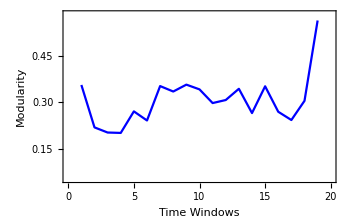
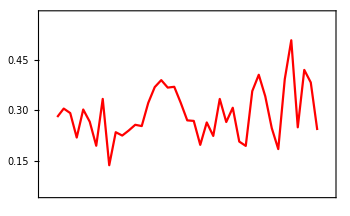
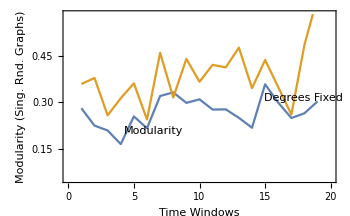
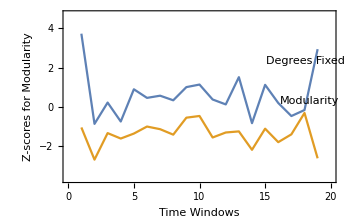

```mathematica
modularityplotrange={0.05246,0.584368};(* MinMax[{modularityvalues4,singlerandomcommmodularityvalues4,singlerandomerdrenmodularityvalues4,modularityvalues42}];*)
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues4}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange}],ListLinePlot[Thread[{Range@win2,modularityvalues42}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},modularityplotrange}]}],
ListLinePlot[{Thread[{Range@win1,singlerandomerdrenmodularityvalues4}],Thread[{Range@win1,singlerandomcommmodularityvalues4}]},Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},modularityplotrange},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Below}]],
ListLinePlot[{Thread[{Range@win1,Zscoresmodularity4[[All,1]]}],Thread[{Range@win1,Zscoresmodularity4[[All,2]]}]},Frame->True,ImagePadding->42,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-scores for Modularity",None},{Style["Time Windows",Blue],None}},ImageSize->350,PlotRange->{{0,win1+1},MinMax[Flatten[Zscoresmodularity4],1]},PlotLabels->Placed[{"Degrees Fixed","Modularity"},{Scaled[1],Above}]]}
```

node numbers should be equal for two different network approaches (fixed step size and fixed bucket size) for the same data.

```mathematica
Print[Style[{"Width Network Nodes for large timewindow - Fixed StepSize",step12},Blue],graphsandnodenumbers1[[All,2]]]
Print[Style[{"Width Network Nodes for large timewindow - Fixed BucketSize",bucketsize3},Blue],graphsandnodenumbers3[[All,2]]]
Print[Style[{"Width Network Nodes for narrow timewindow - Fixed StepSize",step12},Red],graphsandnodenumbers12[[All,2]]]
Print[Style[{"Width Network Nodes for narrow timewindow - Fixed BucketSize",bucketsize32},Red],graphsandnodenumbers32[[All,2]]]

Print[Style[{"Thickness Network Nodes for large timewindow - Fixed StepSize",step21},Blue],graphsandnodenumbers2[[All,2]]]
Print[Style[{"Thickness Network Nodes for large timewindow - Fixed BucketSize",bucketsize4},Blue],graphsandnodenumbers4[[All,2]]]
Print[Style[{"Thickness Network Nodes for narrow timewindow - Fixed StepSize",step22},Red],graphsandnodenumbers22[[All,2]]]
Print[Style[{"Thickness Network Nodes for narrow timewindow - Fixed BucketSize",bucketsize42},Red],graphsandnodenumbers42[[All,2]]]
```

{Width Network Nodes for large timewindow - Fixed StepSize,11}{70,81,84,84,88,86,84,77,82,82,76,78,81,86,85,83,83,87,87}

{Width Network Nodes for large timewindow - Fixed BucketSize,{497,429,414,414,395,404,414,452,424,424,458,446,429,404,409,419,419,400,400}}{70,81,84,84,88,86,84,77,82,82,76,78,81,86,85,83,83,87,87}

{Width Network Nodes for narrow timewindow - Fixed StepSize,11}{56,66,69,70,73,67,68,72,76,78,81,73,66,75,68,62,71,67,70,72,63,72,74,65,67,63,71,74,78,75,78,77,70,66,73,74,78,75,67,78,81}

{Width Network Nodes for narrow timewindow - Fixed BucketSize,{296,251,240,237,227,247,244,230,218,213,205,227,251,221,244,267,234,247,237,230,263,230,224,255,247,263,234,224,213,221,213,215,237,251,227,224,213,221,247,213,205}}{56,66,69,70,73,67,68,72,76,78,81,73,66,75,68,62,71,67,70,72,63,72,74,65,67,63,71,74,78,75,78,77,70,66,73,74,78,75,67,78,81}

{Thickness Network Nodes for large timewindow - Fixed StepSize,1}{23,24,24,15,22,22,19,20,16,19,22,21,22,15,18,20,14,10,12}

{Thickness Network Nodes for large timewindow - Fixed BucketSize,{1511,1448,1448,2317,1580,1580,1829,1738,2172,1829,1580,1655,1580,2317,1931,1738,2482,3475,2896}}{23,24,24,15,22,22,19,20,16,19,22,21,22,15,18,20,14,10,12}

{Thickness Network Nodes for narrow timewindow - Fixed StepSize,1}{23,18,11,10,23,24,15,14,12,12,13,19,20,12,9,17,17,14,15,11,19,16,12,12,12,16,16,12,11,8,8,11,15,17,10,10,9,9,8,8,11}

{Thickness Network Nodes for narrow timewindow - Fixed BucketSize,{720,920,1505,1655,720,690,1103,1182,1379,1379,1273,871,828,1379,1839,974,974,1182,1103,1505,871,1035,1379,1379,1379,1035,1035,1379,1505,2069,2069,1505,1103,974,1655,1655,1839,1839,2069,2068,1504}}{23,18,11,10,23,24,15,14,12,12,13,19,20,12,9,17,17,14,15,11,19,16,12,12,12,16,16,12,11,8,8,11,15,17,10,10,9,9,8,8,11}